## Functions

```mathematica
θ[x_,thresh_]:=If[x<thresh,0,1];
πD[b_,num_,thresh_]:=b θ[num,thresh]+1;
πC[b_,c_,num_,thresh_]:=πD[b,num,thresh]-c/num  θ[num,thresh]-c/thresh (1-θ[num,thresh]);
πintraD[d_,b_,c_,num_,ω_]:=b/d∑_(i=0)^(num-1) ω^i;
πintraC[d_,b_,c_,num_,ω_]:=πintraD[d,b,c,num,ω]-c;
fD[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πD[b,k,thresh]))+(1-p)(∑_(k=0)^(d-1) (Binomial[d-1,k] y^k (1-y)^(d-1-k) πintraD[dintra,bintra,cintra,k,ω]));
fC[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πC[b,c,k+1,thresh]))+(1-p)(∑_(k=0)^(d-1) (Binomial[d-1,k] y^k (1-y)^(d-1-k) πintraC[dintra,bintra,cintra,k+1,ω]));
fbar1[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=x fC[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p]+(1-x)fD[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p];
fbar2[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=y fC[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p]+(1-y)fD[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p];
xdot[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,m_,ω_,p_]:=m x (1-x) (fC[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p] - fD[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p]);
ydot[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,n_,ω_,p_]:=n y (1-y)(fC[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p] - fD[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p]);
```

```mathematica
checkinternal[point_]:=If[point⟦1⟧>0&&point⟦1⟧<1&&point⟦2⟧>0&&point⟦2⟧<1,1,0];
```

```mathematica
plotrange={{-0.02,1.02},{-0.02,1.02}};
```

## Parameters

```mathematica
ClearAll[n,ω,ω1,ω2,r1,r2,d,p]
```

```mathematica
gamea={3,3/4};
gameb={1,3/4};
gamec={1,4/3};
gamed={3,4/3};

d1=5;
d2=5;
d1intra=5;
d2intra=5;
thresh1=1;
thresh2=1;
b=2;
c=1;
bintraforsp1=10;
cintraforsp1=gameb⟦1⟧;
ωforsp1=gameb⟦2⟧//N;

bintraforsp2=10;
cintraforsp2=gameb⟦1⟧;
ωforsp2=gameb⟦2⟧//N;

m=1/8//N;
n=1;
lim=100;
```

## Functions for fluctuations

```mathematica
a=10;
diff=0;
num[t_]:=(Sin[a t-diff ]+1)/2;(*If[Sin[a t]>0,1/(1+A Sin[a t]),1-A Sin[a t]]*)
mean=Mean[Table[num[t],{t,0,20 π,0.0001}]]
(*geomean=GeometricMean[Table[num[t],{t,0,20 π,0.0001}]]*)
```

0.5

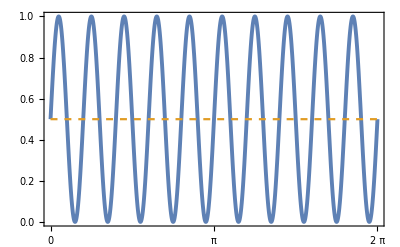

```mathematica
Plot[{num[t],mean},{t,0,2 π},PlotStyle->{{Thickness[0.007]},{Thickness[0.004],Dashed},{Thickness[0.004]}},PlotRange->{Automatic,Automatic},Frame->True,FrameStyle->Thickness[0.0025],FrameTicks->{{Automatic,Automatic},{{0,Pi,2Pi,15Pi,20Pi},None}},ImagePadding->20]
```

## Analysis

```mathematica
plotlis={};
plotdata={};
tlim=100;
For[i=0.1,i≤0.9,i=i+0.1,
For[j=0.1,j≤0.9,j=j+0.1,
sinlistcheck={};
s=Quiet[NDSolve[{
x'[t]== m x[t] (fC[d1,d1intra,y[t],x[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]] - fbar1[d1,d1intra,x[t],y[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]]),y'[t]==n y[t] (fC[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]] - fbar2[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]]),
x[0]==i,y[0]==j},{x,y},{t,0,tlim},MaxStepSize->0.005]];
tabsin=Table[{Evaluate[x[t]/.s]⟦1⟧,Evaluate[y[t]/.s]⟦1⟧},{t,0,tlim}];
AppendTo[plotdata,tabsin];
]
]
```

```mathematica
res[p_,q_,lim_]:=Quiet[NDSolve[{x'[t]== m x[t] (fC[d1,d1intra,y[t],x[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]] - fbar1[d1,d1intra,x[t],y[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,num[t]]),y'[t]==n y[t] (fC[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]] - fbar2[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,num[t]]),x[0]==p,y[0]==q},{x,y},{t,lim}]];
liseval[t_,rep_]:=Evaluate[{x[t],y[t]}/.rep];
```

ReplaceAll::reps: {rep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Clear[blue,red,black];
blue={};
red={};
black={};
For[u=0.0,u≤1.0,u=u+0.01,For[v=0.0,v≤1.0,v=v+0.01,
If[
liseval[lim,res[u,v,lim]]⟦1⟧⟦1⟧>0.9999&&liseval[lim,res[u,v,lim]]⟦1⟧⟦2⟧<0.001,AppendTo[red,{u,v}],If[liseval[lim,res[u,v,lim]]⟦1⟧⟦1⟧<0.001&&liseval[lim,res[u,v,lim]]⟦1⟧⟦2⟧>0.9999,AppendTo[blue,{u,v}],AppendTo[black,{u,v}]]];
]]
```

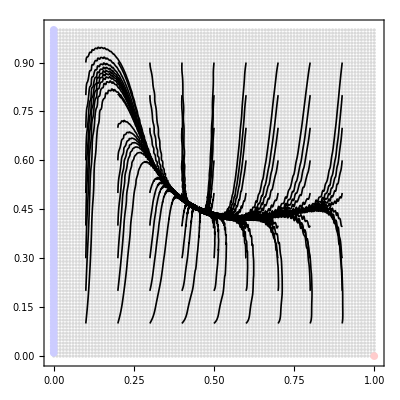

```mathematica
g1=ListPlot[{blue,red,black},PlotStyle->{Lighter[Blue,0.8],Lighter[Red,0.4],Lighter[Gray,0.7]},AspectRatio->1,Frame->True,PlotRange->{{-0.01,1.01},{-0.01,1.01}}];

plotcolors={};
For[i=1,i≤Length[plotdata],i++,
If[Last[plotdata⟦i⟧]⟦1⟧≥0.99&&Last[plotdata⟦i⟧]⟦2⟧≤0.01,AppendTo[plotcolors,{Darker[Red],Thickness[0.003]}],
If[Last[plotdata⟦i⟧]⟦2⟧≥0.99&&Last[plotdata⟦i⟧]⟦1⟧≤0.01,
AppendTo[plotcolors,{Darker[Blue],Thickness[0.003]}],AppendTo[plotcolors,{Black,Thickness[0.003]}]
]
];
]
Show[g1,ListPlot[{blue,red},PlotStyle->{Lighter[Blue,0.8],Lighter[Red,0.8]},AspectRatio->1,Frame->True,PlotRange->plotrange],ListPlot[plotdata,Joined->True,InterpolationOrder->2,AspectRatio->1,PlotRange->plotrange,PlotStyle->plotcolors,Frame->True],
Frame->True,FrameStyle->Thickness[0.0025],ImagePadding->17]
```

## Stability across the range of p

```mathematica
points[z_,q_]:=Table[{p,Cases[Cases[{q,z}/.Quiet[Solve[If[ω1==1&&ω2==1,p (1+(r1-1) z^(n-1)-r1/n (1-z^n)/(1-z))+(1-p) (1+(r2-1) z^(n-1)-r2/n (1-z^n)/(1-z)),p FHauert[z,ω1,q,r1]+(1-p)FHauert[z,ω2,q,r2]]==0&&p (q z (r1-1) (1-z^(n-1))-d)+(1-p)  (q z (r2-1) (1-z^(n-1))-d) ==0&&If[ω1==1&&ω2==1,p (1+(r1-1) z^(n-1)-r1/n (1-z^n)/(1-z))+(1-p) (1+(r2-1) z^(n-1)-r2/n (1-z^n)/(1-z)),p FHauert[z,ω1,q,r1]+(1-p)FHauert[z,ω2,q,r2]]==p (q z (r1-1) (1-z^(n-1))-d)+(1-p)  (q z (r2-1) (1-z^(n-1))-d),{q,z}]],{Except[_Complex],Except[_Complex]}],
Except[{}]]}
,{p,0,1,0.05}
];
```

```mathematica
fixedomega1=points[z,q];
```

```mathematica
onlyinternalomega1=fixedomega1⟦1;;,{1}⟧;
For[i=1,i≤Length[fixedomega1],i++,
For[j=1,j≤Length[fixedomega1⟦i,2⟧],j++,
If[checkinternal[fixedomega1⟦i,2⟧⟦j⟧]==1,AppendTo[onlyinternalomega1⟦i⟧,fixedomega1⟦i,2⟧⟦j⟧]]
]
]
```

```mathematica
JacobianMatrix[eqs_,var_]:={{D[eqs⟦1⟧,var⟦1⟧],D[eqs⟦1⟧,var⟦2⟧]},{D[eqs⟦2⟧,var⟦1⟧],D[eqs⟦2⟧,var⟦2⟧]}}
```

```mathematica
ClearAll[p,F];
G[q_,z_]:={-z q (1-q) (p F[z,ω1,q,r1]+(1-p)F[z,ω2,q,r2]),p (-(1-z) (q z (r1-1) (1-z^(n-1))-d) )+(1-p) (-(1-z) (q z (r2-1) (1-z^(n-1))-d) )};
J=FullSimplify[JacobianMatrix[G[q,z],{q,z}]/.{(p F[z,ω1,q,r1]+(1-p)F[z,ω2,q,r2])->0}];
F[z_,ω_,q_,r_]:=-(r (-z^n+(1-q (1-z) (1-ω))^n))/(n (1-z-q (1-z) (1- ω)))+1+(r-1) z^(n-1) ;
```

```mathematica
eigenomega1={};
For[i=1,i≤Length[onlyinternalomega1],i++,
AppendTo[eigenomega1,{
onlyinternalomega1⟦i⟧⟦1⟧,
Length[onlyinternalomega1⟦i⟧]-1,Table[{Eigenvalues[J//.{q->onlyinternalomega1⟦i,k⟧⟦1⟧,z->onlyinternalomega1⟦i,k⟧⟦2⟧,p->onlyinternalomega1⟦i⟧⟦1⟧}]},{k,2,Length[onlyinternalomega1⟦i⟧]}],
Table[{Tr[J//.{q->onlyinternalomega1⟦i,k⟧⟦1⟧,z->onlyinternalomega1⟦i,k⟧⟦2⟧,p->onlyinternalomega1⟦i⟧⟦1⟧}]},{k,2,Length[onlyinternalomega1⟦i⟧]}],
Table[{Det[J//.{q->onlyinternalomega1⟦i,k⟧⟦1⟧,z->onlyinternalomega1⟦i,k⟧⟦2⟧,p->onlyinternalomega1⟦i⟧⟦1⟧}]},{k,2,Length[onlyinternalomega1⟦i⟧]}]
}]
]
```

```mathematica
eigenomega1//MatrixForm
```

(0. | 1 | {{{0.191374,0.048948}}} | {{0.240322}} | {{0.00936738}}
0.05 | 1 | {{{0.10546+0.0764156 ⅈ,0.10546-0.0764156 ⅈ}}} | {{0.210921}} | {{0.0169612}}
0.1 | 1 | {{{0.0869914+0.134394 ⅈ,0.0869914-0.134394 ⅈ}}} | {{0.173983}} | {{0.0256294}}
0.15 | 1 | {{{0.0666807+0.175769 ⅈ,0.0666807-0.175769 ⅈ}}} | {{0.133361}} | {{0.0353411}}
0.2 | 1 | {{{0.0458396+0.20906 ⅈ,0.0458396-0.20906 ⅈ}}} | {{0.0916792}} | {{0.0458074}}
0.25 | 1 | {{{0.0252227+0.236728 ⅈ,0.0252227-0.236728 ⅈ}}} | {{0.0504454}} | {{0.0566763}}
0.3 | 1 | {{{0.00520987+0.260017 ⅈ,0.00520987-0.260017 ⅈ}}} | {{0.0104197}} | {{0.0676359}}
0.35 | 1 | {{{-0.0140386+0.279728 ⅈ,-0.0140386-0.279728 ⅈ}}} | {{-0.0280772}} | {{0.0784448}}
0.4 | 1 | {{{-0.0324824+0.296438 ⅈ,-0.0324824-0.296438 ⅈ}}} | {{-0.0649649}} | {{0.0889308}}
0.45 | 1 | {{{-0.0501439+0.310585 ⅈ,-0.0501439-0.310585 ⅈ}}} | {{-0.100288}} | {{0.0989777}}
0.5 | 1 | {{{-0.0670757+0.32251 ⅈ,-0.0670757-0.32251 ⅈ}}} | {{-0.134151}} | {{0.108512}}
0.55 | 1 | {{{-0.083344+0.332485 ⅈ,-0.083344-0.332485 ⅈ}}} | {{-0.166688}} | {{0.117492}}
0.6 | 1 | {{{-0.0990185+0.340726 ⅈ,-0.0990185-0.340726 ⅈ}}} | {{-0.198037}} | {{0.125899}}
0.65 | 1 | {{{-0.114169+0.34741 ⅈ,-0.114169-0.34741 ⅈ}}} | {{-0.228337}} | {{0.133728}}
0.7 | 1 | {{{-0.12886+0.352682 ⅈ,-0.12886-0.352682 ⅈ}}} | {{-0.257719}} | {{0.140989}}
0.75 | 1 | {{{-0.143153+0.356657 ⅈ,-0.143153-0.356657 ⅈ}}} | {{-0.286307}} | {{0.147697}}
0.8 | 1 | {{{-0.157106+0.359432 ⅈ,-0.157106-0.359432 ⅈ}}} | {{-0.314212}} | {{0.153874}}
0.85 | 1 | {{{-0.17077+0.361082 ⅈ,-0.17077-0.361082 ⅈ}}} | {{-0.34154}} | {{0.159543}}
0.9 | 1 | {{{-0.184192+0.361669 ⅈ,-0.184192-0.361669 ⅈ}}} | {{-0.368385}} | {{0.164732}}
0.95 | 1 | {{{-0.197417+0.36124 ⅈ,-0.197417-0.36124 ⅈ}}} | {{-0.394834}} | {{0.169468}}
1. | 1 | {{{-0.210483+0.359829 ⅈ,-0.210483-0.359829 ⅈ}}} | {{-0.420966}} | {{0.17378}})

```mathematica
Manipulate[Plot[{(Sin[a t ]+1)/2,0,0.05,0.35,1.0,1.2,mean,(Sin[a t+π/2 ]+1)/2,(Sin[a t-π/2 ]+1)/2},{t,0,2 π},PlotStyle->{{Thickness[0.007]},{Black,Thickness[0.002]},{Opacity[0]},{Opacity[0]},{Opacity[0]},{Black,Thickness[0.002]},{Black,Thickness[0.005]},{Thickness[0.007],Dashed,Darker[Orange]},{Thickness[0.007],Dotted,Darker[Magenta]}},Frame->True,FrameStyle->Thickness[0.0025],PlotRange->{{-0.1,2 π+0.1},{-0.1,1.1}},FrameTicks->{{{{0,"0.0"},{1,"1.0"},{2,"2.0"}},Automatic},{{0,π,2Pi},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{Text[Style["Time",Black,24]],None},ImagePadding->55,Filling->{2->{{3},Lighter[Orange,0.5]},3->{{4},Lighter[Red,0.8]},4->{{5},Lighter[Blue,0.8]}(*,5->{{6},Lighter[Yellow,0.5]}*)}],{{a,1},{0.1,1,10}}]
```